# 2D Computational Model for Invasion Sports

## Willem Nielsen

## Utilities

```mathematica
lightBeige = RGBColor[1.,0.9920042725261311,0.8800030518043793];
```

```mathematica
SetOptions[EvaluationNotebook[],Background-> lightBeige]
```

```mathematica
ResourceFunction["DarkMode"][]
```

```mathematica
ClearAll["Global`*"]
```

## Functions

### Initialization

```mathematica
getHad[turn_]:= If[turn == "α", homeAwayDistance, -homeAwayDistance]
```

```mathematica
getPoint[center_,angle_,radius_]:=center+radius*AngleVector[angle]
getAwayPoints[homePoints_, homeAwayDistance_:1/10]:= Map[{#[[1]],#[[2]] + homeAwayDistance}&, homePoints, {2}]
getRecPoints[point_, size_]:={getPoint[point, 225Degree, size], getPoint[point, 45Degree, size]}
getTriPoints[point_, size_]:=
{getPoint[point, 88Degree, size - 1/12],getPoint[point, 210 Degree, size], getPoint[point, 330Degree, size ]}
```

```mathematica
getPlayerLoc[team_, i_]:= If[team == "home", homePlayers[[i]], awayPlayers[[i]]]
getHomePlayers[startCol_:1, spacing_:1, nPlayers_:3, row_:1]:= Module[{hidxs},
hidxs = NestList[#+spacing&, startCol, nPlayers - 1];
homeLocs[[row, hidxs]]
]

getAwayPlayers[startCol_:1, spacing_:1, nPlayers_:3, row_:-1]:=Module[{idxs},
idxs = NestList[#+spacing&, startCol, nPlayers - 1];
awayLocs[[row, idxs]]
]
```

```mathematica
initializePlayers[nHome_:3, nAway_:3,hspacing_:ballSpeed, aspacing_:ballSpeed, hStartCol_:1, aStartCol_:1, homeStartRow_:1, awayStartRow_:-1]:=
Module[{hidxs, aidxs}, 
hidxs = NestList[#+hspacing&, hStartCol, nHome - 1];
aidxs = NestList[#+aspacing&, aStartCol, nAway - 1];
{homeLocs[[homeStartRow, hidxs]], awayLocs[[awayStartRow, aidxs]]}
]
```

### Visualization

```mathematica
Options[showGame] = {highlightPoints->{}};
showGame[{homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_, res_}, OptionsPattern[{Graphics, showPlay, showGame}]]:=Module[{hpRecs, apTris, allShapes, dribbler,ball, g},
	hpRecs = Rectangle@@getRecPoints[#, playerSize]&/@ homePlayers;
	apTris = N/@Polygon@getTriPoints[#,playerSize]&/@ awayPlayers;
	ball = Disk[ballLoc, ballSize];
	g = Graphics[{FaceForm@White,background, FaceForm@LightRed, endzone, FaceForm@Gray, Point@N@Flatten[OptionValue[points], 1], FaceForm@Blue, hpRecs,FaceForm@Red,apTris, Green, ball,
	Red, Point@OptionValue[highlightPoints]}, ImageSize->OptionValue[ImageSize]]
(*	If[OptionValue[showEvaluation], Column[g, getEvaluation[{homePlayers, awayPlayers, ballLoc, turn, guardedCount, res}]]]*)
]
```

#### Show one move

```mathematica
getObjectMovementFrames[start_, end_, frames_:20]:= Subdivide[start, end,frames]

getMoveFrames[gameStateStart_, gameStateEnd_, frameRate_:10]:= Module[{go1, go2, gf1, gf2, turn, gc, hpl, apl, objectFrames, gameStatesFlat, 
gameObjectFrames, gameStates, res}, 
  go1 = gameStateStart[[;;2]];
  go2 = gameStateEnd[[;;2]];
  gf1 = Append[Flatten[go1, 1], gameStateStart[[3]]];
  gf2 = Append[Flatten[go2,1], gameStateEnd[[3]]];
  turn = gameStateEnd[[4]]; gc = gameStateEnd[[5]];res = gameStateEnd[[6]];
  objectFrames = MapThread[getObjectMovementFrames[#1, #2, frameRate]&, {gf1, gf2}];
  gameStatesFlat = Transpose[objectFrames];
  hpl = Length@homePlayers; apl = Length@awayPlayers;
  gameObjectFrames = {#[[;;hpl]], #[[hpl+1;;hpl+apl]],#[[hpl+apl+1]]}&/@ gameStatesFlat;
  gameStates = Join[#, {turn, gc, res}]& /@ gameObjectFrames
  ]

getMoveFrameGraphics[gameStateStart_, gameStateEnd_, frameRate_:10]:= Module[{moveFrames}, 
  moveFrames = getMoveFrames[gameStateStart, gameStateEnd, frameRate];
  showGame/@ moveFrames
  ]

showMove[gameStateStart_, gameStateEnd_, frameRate_:20]:= Module[{graphicsFrames}, 
  graphicsFrames = getMoveFrameGraphics[gameStateStart, gameStateEnd, frameRate];
  ListAnimate[graphicsFrames, DefaultDuration->1, AnimationRepetitions->1]
 ]
```

#### Show entire play

```mathematica
alignFrames[attackers_, defenders_, delay_:5]:=Module[{},
defendersDelayed = Join[Table[First@defenders, delay], defenders];
lengthDiff = Length@attackers - Length@defendersDelayed;
Which[
lengthDiff == 0, {attackers, defendersDelayed},
Positive[lengthDiff], {attackers, Join[defendersDelayed, Table[Last@defendersDelayed, lengthDiff]]},
Negative[lengthDiff], {Join[attackers, Table[Last@attackers, -1*lengthDiff]], defendersDelayed}
]]

mergeGames[attackerGameState_,defenderGameState_]:=  
{attackerGameState[[1]], defenderGameState[[2]], attackerGameState[[3]], attackerGameState[[4]], defenderGameState[[5]], defenderGameState[[6]]}
```

```mathematica
getPlayGraphicFrames[moves_, op___]:= Module[{attackingTeam, defendingTeam, movePairs, attackingMovePairs, defendingMovePairs, attackingFrames, defendingFrames, allFrames, mergedFrames,
graphics}, 
attackingTeam =moves[[1, 4]]; defendingTeam = flip@attackingTeam;
movePairs = Partition[moves, 2, 1];
attackingMovePairs  = Select[movePairs, #[[2, 4]] == defendingTeam&];
defendingMovePairs = Select[movePairs, #[[2, 4]] == attackingTeam&];
attackingFrames =  Flatten[getMoveFrames@@@ attackingMovePairs, 1];
defendingFrames = Flatten[getMoveFrames@@@ defendingMovePairs, 1];
allFrames =alignFrames[attackingFrames, defendingFrames];

mergedFrames = MapThread[mergeGames[#1, #2]&, allFrames];
graphics = showGame[#, op]& /@ mergedFrames
]
```

```mathematica
Options[showPlay] = {duration->5, points->{}};
showPlay[moves_,op___]:= Module[{frames}, 
frames = getPlayGraphicFrames[moves, op];
ListAnimate[frames, DefaultDuration->5, AnimationRepetitions->1]
]
```

```mathematica
getVideo[play_,frameRate_:15, op___]:= Module[{frames}, 
frames = getPlayGraphicFrames[play];
FrameListVideo[frames, FrameRate->frameRate]
]
```

#### Other

```mathematica
overlayAttackingMove[move_, gameState_, op___]:= showGame[ReplacePart[gameState, {1->Most[move], 3->Last[move]}] , op]
overlayDefendingMove[move_, gameState_]:= showGame[ReplacePart[gameState, 2->move]]
```

```mathematica
showAttackingMove[{players__, ballLoc_}, team_, OptionsPattern[{showPlay, showGame}]]:=Module[{hpRecs, apTris, allShapes, dribbler},
playerShapes = If[team == "home",  Rectangle@@getRecPoints[#, playerSize]&/@ {players}, 
 N@Polygon@getTriPoints[#,playerSize]&/@ awayPlayers];
ball = Disk[ballLoc, ballSize];
color = If[team== "home", Blue, Red];
Graphics[{FaceForm@White,background, FaceForm@Gray, Point@N@OptionValue[points], FaceForm@color, playerShapes, Green, ball,
	Red, Point@OptionValue[highlightPoints]}]]
```

```mathematica
showDefensiveMove[players_, team_, OptionsPattern[{showPlay, showGame}]]:=Module[{hpRecs, apTris, allShapes, dribbler},
playerShapes = If[team == "home",  Rectangle@@getRecPoints[#, playerSize]&/@ players, 
 N/@Polygon@getTriPoints[#,playerSize]&/@ players];
color = If[team== "home", Blue, Red];
Graphics[{FaceForm@White,background, FaceForm@Gray, Point@N@OptionValue[points], FaceForm@color, playerShapes,
	Red, Point@OptionValue[highlightPoints]}]]
```

### Game Logic

#### General

```mathematica
flip[turn_]:= Replace[turn, {"α"->"β","β"->"α"}]
```

```mathematica
getAttackerTurn[{homePlayers_, awayPlayers_ , ballLoc_, turn_, gc_, res_}] := 
    Which[
	MemberQ[homePlayers, ballLoc], "α",
	MemberQ[awayPlayers, ballLoc], "β",
	True, "α"]
```

```mathematica
flipturn[gameState_]:= ReplaceAll[gameState, {"α"->"β","β"->"α"}]
```

#### Booleans

```mathematica
guardedQ[{homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_, res_}]:=
  MemberQ[awayPlayers, {ballLoc[[1]], ballLoc[[2]]+1/10}] || MemberQ[homePlayers, {ballLoc[[1]], ballLoc[[2]]-1/10}]
```

```mathematica
turnoverQ[{homePlayers_, awayPlayers_ , {ballX_, ballY_}, turn_, guardedCount_, res_}]:= 
Module[{maySteal, awaySteal, homeSteal},
maySteal = guardedCount == stealDifficulty;
awaySteal = MemberQ[awayPlayers, {ballX,ballY + homeAwayDistance}];
homeSteal =MemberQ[homePlayers, {ballX,ballY - homeAwayDistance}];
If[(maySteal && awaySteal) || (maySteal && homeSteal), True, False]
]
```

```mathematica
gameOverQ[gameState_]:=Module[{}, 
touchdownQ[gameState]|| interceptionQ[gameState] || turnoverQ[gameState]
]
```

```mathematica
interceptionQ[defenders_, {ballX_, ballY_}, turn_:"α"]:=Module[{},
had = getHad[turn];
MemberQ[defenders, {ballX,ballY + had}]
]
```

```mathematica
touchdownQ[{ballX_, ballY_}, turn_:"α"]:= Module[{}, 
ez = If[turn == "α", homeEndZoneY, awayEndZoneY];
ballY == ez
]
```

```mathematica
attackerTurnQ[gameState_]:= Module[{},
{hps, aps, ballLoc, turn ,gs, res} = gameState;
(MemberQ[hps, ballLoc]&& turn == "α") || (MemberQ[aps, ballLoc]&& turn == "β" )
]
```

#### Evaluating State

```mathematica
getEZ[turn_]:= If[turn == "α", {homeEndZoneY, awayEndZoneY},{awayEndZoneY, homeEndZoneY} ]
```

```mathematica
evaluateAttackingState[move_, gameState_]:=Module[{},
turn = getAttackerTurn[gameState]; defenders = getDefenders[gameState];had = getHad[turn];
ballLoc = Last[move]; attackers = Most[move];
{hez, aez} = getEZ[turn];
Which[
interceptionQ[defenders, ballLoc], ballLoc[[2]]+had - hez,
	(*td*)
	MemberQ[attackers,ballLoc]&&ballLoc[[2]] == hez, 100,
(*The further up the field the better*)
MemberQ[attackers,ballLoc], ballLoc[[2]] - aez+2/10,
	True, 0
]]
```

#### Getting Moves

```mathematica
getMovesBounded[currentPoint_, speed_:playerSpeed]:=Module[{allPoints},
  allPoints = Map[getPoint[currentPoint, #, speed]&, directions];
  Select[allPoints, RegionMember[gamePoly, #]&]
]
getMovesBoundedStatic[currentPoint_, speed_:1]:=Module[{allPoints},
  allPoints = Append[Map[getPoint[currentPoint, #, speed]&, directions], currentPoint];
  Select[allPoints, RegionMember[gamePoly, #]&]
]
getMovesBoundedExcept[players_, pg_, moveFunc_:getMovesBounded]:= Insert[(moveFunc/@Delete[players, pg]), {players[[pg]]}, pg]
```

```mathematica
getDefenders[{homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_, res_}]:= If[MemberQ[homePlayers, ballLoc], awayPlayers, homePlayers]
```

```mathematica
getAttackers[{homePlayers_, awayPlayers_ , ballLoc_, turn_, gc_, res_}]:= If[MemberQ[homePlayers, ballLoc], homePlayers, awayPlayers]
```

```mathematica
getAttackerGameState[move_, gameState_ ]:=Module[{},
 {h, a, ballLoc, t, gc, res}  = gameState;
defenders = getDefenders[gameState];
turn = getAttackerTurn[gameState];
result = Which[
interceptionQ[defenders, Last[move]], -100,
touchdownQ[Last[move]],100,
True, 0
];
replaceIdx = If[turn == "α", 1, 2];
ReplacePart[gameState, {replaceIdx->Most[move], 3->Last[move], 4->flip@turn, 6->result}]
]
```

```mathematica
getDefenderGameState[move_, {homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_, res_} ]:=Module[{},
replaceIdx = If[turn == "α", 1, 2];
ReplacePart[{homePlayers, awayPlayers , ballLoc, flip@turn, guardedCount, res}, replaceIdx->move]
]
```

```mathematica
getBallMoves[ballLoc_, turn_:"α"]:= Module[{allPoints},
  If[turn == "α", Select[Flatten[homeLocs, 1], EuclideanDistance[ballLoc, #]<= ballSpeed &], 
  Select[Flatten[awayLocs, 1], EuclideanDistance[ballLoc, #]<= ballSpeed &]]
]
```

```mathematica
turnover[{homePlayers_, awayPlayers_ , {ballX_, ballY_}, turn_, guardedCount_, res_}]:= 
Module[{maySteal, awayStealY, homeStealY, awaySteal, homeSteal},
maySteal = guardedCount == stealDifficulty;
awayStealY = ballY+homeAwayDistance;
homeStealY =  ballY-homeAwayDistance;
awaySteal = MemberQ[awayPlayers, {ballX,awayStealY}];
homeSteal =MemberQ[homePlayers, {ballX,homeStealY}];
Which[
maySteal&&awaySteal,  {homePlayers, awayPlayers, {ballX, awayStealY}, "β", -1},
maySteal&&homeSteal,  {homePlayers, awayPlayers, {ballX, homeStealY}, "α", -1},
awaySteal||homeSteal,  {homePlayers, awayPlayers, {ballX, ballY}, turn, guardedCount+1},
True, {homePlayers, awayPlayers , {ballX, ballY}, turn, 0}
]]
```

#### Choosing Moves

```mathematica
getpg[attackers_, ballLoc_] := First[FirstPosition[attackers, ballLoc]]
```

```mathematica
getPassLocs[ginfo_, bmoves_]:=  If[ginfo["turntype"] == "attacker", bmoves, (getOpp[#,-ginfo["had"]]&/@ bmoves)];
```

```mathematica
getPasses[cuts_]:= Append[cuts, #]&/@ cuts
```

```mathematica
getOpp[loc_, had_]:= {loc[[1]], loc[[2]]+ had}
```

```mathematica
getGameInfo[gameState_]:= Module[{turn, ball,had, aturn, attackers ,pg, bmoves, turntype, bdmoves},
turn = gameState[[4]]; ball = gameState[[3]]; had = getHad[turn];
aturn = getAttackerTurn[gameState];
attackers = getAttackers[gameState];
pg = getpg[attackers, ball];
bmoves = getBallMoves[ball,aturn];
turntype = If[aturn == turn, "attacker", "defender"];
(*bmoves = If[turntype == "attacker", bmoves, (getOpp[#, -had]&/@ bmoves)]; *)
<|"had"->had,"turn"->turn,
"bmoves"->bmoves,
"defenders"->getDefenders[gameState],
"attackers"->attackers, "pg"->pg, "pgLoc"->attackers[[pg]], "aturn"->aturn, "aoffball"->Delete[attackers, pg],
"turntype"->If[aturn == gameState[[4]], "attacker", "defender"]|>
]
```

```mathematica
getNearestMoveAttacker[taken_, mymoves_, player_, ginfo_]:= Module[{npass, nmove},
npass = First@Nearest[ginfo["bmoves"], player];
nmove =Nearest[Complement[mymoves, taken], npass, 1]
]
```

```mathematica
getNearestMoveDefender[taken_, mymoves_, player_, ginfo_]:= Module[{npass, nmove},
npass = First@Nearest[ginfo["passLocs"], player];
nmove =Nearest[Complement[mymoves, taken], npass, 1]
]
```

```mathematica
getFurthest[moves_, n_:1]:= MaximalBy[moves, #[[2]]&, UpTo@n]
```

```mathematica
sowCuts[{taken_, ginfo_}, player_]:= Module[{mymoves, passes,npass, nmove, open, furthest},
mymoves = getMovesBoundedStatic[player];
passes = Complement[Intersection[ginfo["bmoves"], mymoves], taken];
If[passes == {}, 
nmove = getNearestMoveAttacker[taken, mymoves, player, ginfo];
 Sow[nmove];{Join[taken, nmove], ginfo},
open = Select[passes,  !interceptionQ[ginfo["defenders"], #, ginfo["aturn"]]&];
If[open == {}, open = passes];
furthest =  getFurthest[open, 3];
Sow[furthest]; {Join[taken, furthest], ginfo}
]]
```

```mathematica
moveAttackers[gameState_,ginfo_, nChoices_:3]:= Module[{reaped,  pmovesoffball, pmoves, pstates, moves, best}, 
reaped = Reap[FoldList[sowCuts, {{ginfo["pgLoc"]}, ginfo}, ginfo["aoffball"]]];
pmovesoffball = reaped[[2, 1]];
pmoves = Insert[pmovesoffball, {ginfo["pgLoc"]}, ginfo["pg"]];
Echo[pmoves];
(*pstates = Table[Map[RandomChoice, pmoves, 1], 3];*)
pstates = Tuples[pmoves];
Echo[pstates];
moves = Union@Flatten[getPasses/@ pstates, 1];
(*Echo[moves];*)
(*Echo[overlayAttackingMove[#, gameState]&/@ moves];*)
best = TakeLargestBy[moves, evaluateAttackingState[#, gameState]&, UpTo@nChoices]; 
best
]
```

```mathematica
sowGuards[{taken_, ginfo_}, player_]:= Module[{mymoves, guards, nmove, furthest},
mymoves = getMovesBoundedStatic[player];
guards = Complement[Intersection[ginfo["passLocs"], mymoves], taken];
If[guards == {}, 
nmove = getNearestMoveDefender[taken, mymoves, player, ginfo];
 Sow[nmove];{Join[taken, nmove], ginfo},
furthest =  getFurthest[guards, 1];
Sow[furthest]; {Join[taken, furthest], ginfo}
]]
```

```mathematica
moveDefenders[gameState_,ginfo_, nChoices_:3]:= Module[{ reaped, pmoves},  
reaped = Reap[FoldList[sowGuards, {{}, ginfo}, ginfo["defenders"]]];
pmoves = reaped[[2, 1]];
First/@pmoves
]
```

```mathematica
getBestMove[gameState_, op___]:= Module[{amoves, ginfo, ags, bdm},
{homePlayers, awayPlayers , ballLoc, turn, guardedCount, result} = gameState;
If[result!=0, Return[{}],
ginfo = getGameInfo[gameState];
amoves = moveAttackers[gameState,ginfo, 10];AssociateTo[ginfo, "passLocs"-> getPassLocs[ginfo, amoves[[All, -1]]]];
If[ginfo["turntype"] == "attacker", 
ags = getAttackerGameState[First@amoves,gameState],
bdm = moveDefenders[gameState,ginfo]; 
getDefenderGameState[bdm, gameState]
]]]
```

```mathematica
getPlay[initialGameState_,n_:10, iterator_:getBestMoveFast]:= 
Most@NestWhileList[iterator, initialGameState, # != {}&,1, n];
```

### Development

#### Ideas

Idea for smarter Defense: The idea would be that you have the defenders look two moves deep and see where all the ball locs are. So then there is a question of do you want the defenders to simply ignore time and guard the most dangerous positions or what would be better is to have the defenders evaluate the state at further nodes and basically go to a place where they can block the most dangerous threats if that makes sense. 

Search the tree of attacker moves to n depth. So that means having a function like:

```mathematica
moveAttackersTree[gameState_, ginf0_, depth_]:= "TODO"
```

Again what option is then to just get the ball locs from this function and do exactly what we’re doing now. A cooler thing would be to have them go to a point where they can block the future points. So if depth = 2 and you see a ball loc that is dangerous. I don’t know I think for now just ignoring time will actually be fine.

So what I’m thinking of doing here is folding this move attackers and sowing the result. Another option is just to have it be a pure iterator. I think both could work.

```mathematica
sowAttackerMoves[ginfo_, gameState_]:= "TODO"
```

One question is should we distinguish depth while sowing? That may be useful in the future.

I still think we would want to have it be some sort of nest list function. I don’t think this is a sow type thing tbh

```mathematica
moveAttackersTree[gameState_, ginf0_, depth_]:= Nest
```

```mathematica
moveAttackersList[gpacks_]:= Map[moveAttackers, gpacks, {1}]
```

```mathematica
g[x_] := {x*10, x*-10}
```

```mathematica
f[x_] := Map[g, x, {1}]
```

```mathematica
nl = NestList[f, {1}, 3]
```

{{1},{{10,-10}},{{{100,-100},{-100,100}}},{{{{1000,-1000},{-1000,1000}},{{-1000,1000},{1000,-1000}}}}}

```mathematica
Flatten[nl]
```

{1,10,-10,100,-100,-100,100,1000,-1000,-1000,1000,-1000,1000,1000,-1000}

```mathematica
moveAttackers[{gameState_,ginfo_}]:= Module[{reaped,  pmovesoffball, pmoves, pstates, moves, best}, 
reaped = Reap[FoldList[sowCuts, {{ginfo["pgLoc"]}, ginfo}, ginfo["aoffball"]]];
pmovesoffball = reaped[[2, 1]];
pmoves = Insert[pmovesoffball, {ginfo["pgLoc"]}, ginfo["pg"]];
pstates = Table[Map[RandomChoice, pmoves, 1], 3];
moves = Flatten[getPasses/@ pstates, 1];
best = TakeLargestBy[moves, evaluateAttackingState[#, gameState]&, UpTo@nChoices]
]
```

We actually need to move the defenders to get the proper attacker moves so we need something like this

```mathematica
moveAttackersAndDefenders[gameState_]:= Module[{}, 
ginfo = getGameInfo[gameState];
amoves = moveAttackers[gameState,ginfo, 10];
AssociateTo[ginfo, "passLocs"-> getPassLocs[ginfo, amoves[[All, -1]]]];
dm = moveDefenders[gameState, ginfo];
getDefenderGameState[dm, #]&/@ ags
]
```

```mathematica
gss = moveAttackersAndDefenders[initialGameState];
ginfos = getGameInfo/@ gss;
amovesList = MapThread[moveAttackers[#1, #2]&, {gss, ginfos}];
AssociateTo[ginfo, "passLocs"-> getPassLocs[ginfo, amoves[[All, -1]]]];
```

#### Running

Basically I just need a getBestMoves, but it only generates multiple moves for the attackers

```mathematica
getBestGamesList[gameStates_, depth_]:=Map[getBestGames, gameStates, {-3}]
```

```mathematica
{gs}->{{gs1, gs2, gs3}}->{gs1a, gs1b}, {gs2a, gs2b}, {gs3a, gs3b}
```

The only change we need to make to best move is to have it generate multiple attacker moves

```mathematica
ClearAll@getBestGames
```

```mathematica
getBestGame[gameState_]:= Module[{result, amoves, ginfo, ags,ams2, passLocs, bdm},
result = gameState[[-1]];
If[result!=0, Return[{}],
ginfo = getGameInfo[gameState];
amoves = moveAttackers[gameState,ginfo, 3];
ags = getAttackerGameState[#,gameState]&/@ amoves;
Echo[ags];
(*Echo[showGame/@ ags];*)
If[ginfo["turntype"] == "attacker", First@ags,
(*Echo[overlayAttackingMove[#, gameState]&/@ amoves];*)
ams2 = moveAttackers[#, getGameInfo[#], 3]&/@ ags;
(*Echo[Column@ams2];*)
(*Echo[MapThread[overlayAttackingMove[#1, #2]&, {ams2[[3]], Table[ags[[3]], 3]}]];*)
aams = Prepend[ams2, amoves];
passLocs =  Flatten[aams[[All,All,  -1]], 1];
Echo[aams[[1, 2]]];
(*Echo[overlayAttackingMove[#, gameState]&/@ Flatten[aams, 1]];*)
(*Echo[showGame[gameState, points->{passLocs}]];*)
bdm = moveDefenders[gameState,passLocs]; 
getDefenderGameState[bdm, gameState]
]]]
```

```mathematica
getGameStateTree[iterator_, start_, n_:3]:= NestList[iterator, start, n]
```

```mathematica
getPasses[states_]:= MapThread[Append[#1, #1[[#2]]]&, {states, Range[Length@states]}]
```

```mathematica
getStates[pms_, pm_]:= Module[{i, other}, 
i = FirstPosition[pms, pm];
other = First/@ DeleteCases[pms, pm];
Insert[other, #, {i, {-1}}]&/@ pm
]
```

```mathematica
getNearestMoveAttacker[taken_, mymoves_, player_, ginfo_]:= Module[{npass, nmove},
npass = First@Nearest[ginfo["bmoves"], player];
nmove =Nearest[Complement[mymoves, taken], npass, 1]
]
```

```mathematica
getNearestMoveDefender[taken_, mymoves_, player_, passLocs_]:= Module[{npass, nmove},
npass = First@Nearest[passLocs, player];
nmove =Nearest[Complement[mymoves, taken], npass, 1]
]
```

```mathematica
sowCuts[{taken_, ginfo_}, player_]:= Module[{mymoves, passes,npass, nmove, open, furthest},
mymoves = getMovesBoundedStatic[player];
passes = Complement[Intersection[ginfo["bmoves"], mymoves], taken];
If[passes == {}, 
nmove = getNearestMoveAttacker[taken, mymoves, player, ginfo];
 Sow[nmove];{Join[taken, nmove], ginfo},
If[ginfo["turntype"] == "attacker",
open = Select[passes,  !interceptionQ[ginfo["defenders"], #, ginfo["aturn"]]&];
If[open == {}, open = passes],
open = passes];
furthest =  getFurthest[open, 3];
Sow[furthest]; {Join[taken, furthest], ginfo}
]]
```

```mathematica
moveAttackers[gameState, ginfo, nChoices] =
```

```mathematica
moveAttackers[gameState_,ginfo_, nChoices_:3]:=  Module[{reaped,  pmovesoffball, pmoves, pstates, moves, best},
reaped = Reap[FoldList[sowCuts, {{ginfo["pgLoc"]}, ginfo}, ginfo["aoffball"]]];
pmovesoffball = reaped[[2, 1]];
pmoves = Insert[pmovesoffball, {ginfo["pgLoc"]}, ginfo["pg"]];
pstates = Union@Flatten[getStates[pmoves, #]&/@ pmoves,1];
best = TakeLargestBy[pstates, evaluateAttackingState[#, gameState]&, UpTo@nChoices]
]
```

```mathematica
sowGuards[{taken_, passLocs_}, player_]:= Module[{mymoves, guards, nmove, furthest},
mymoves = getMovesBoundedStatic[player];
guards = Complement[Intersection[passLocs, mymoves], taken];
If[guards == {}, 
nmove = getNearestMoveDefender[taken, mymoves, player, passLocs];
 Sow[nmove];{Join[taken, nmove], passLocs},
furthest =  getFurthest[guards, 1];
Sow[furthest]; {Join[taken, furthest], passLocs}
]]
```

```mathematica
moveDefenders[gameState_,passLocs_]:= Module[{ reaped, pmoves},  
reaped = Reap[FoldList[sowGuards, {{}, passLocs}, getDefenders[gameState]]];
pmoves = reaped[[2, 1]];
First/@pmoves
]
```

```mathematica
replaceGames[games_]:=Module[{},
ReplaceAll[games, {hps_, aps_, bl_, turn_, gc_, res_}:>getBestGames[{hps, aps, bl, turn, gc, res}]]
]
```

```mathematica
ClearAll@moveAttackers
```

```mathematica
bg = getBestGame@initialGameState
```

{{{2,(√3)/2},{7/2,√3},{4,(√3)/2}},{{2,1/10+(7 √3)/2},{3,1/10+(7 √3)/2},{4,1/10+(7 √3)/2}},{7/2,√3},β,0,0}

```mathematica
moveAttackers[bg, getGameInfo[bg]]
```

{{{3/2,√3},{7/2,√3},{9/2,√3},{3/2,√3}},{{3/2,√3},{7/2,√3},{9/2,√3},{7/2,√3}},{{3/2,√3},{7/2,√3},{9/2,√3},{9/2,√3}}}

```mathematica
ams = moveAttackers[play3[[8]], getGameInfo[play3[[8]]]]
```

{{{1,(3 √3)/2},{3,(3 √3)/2},{4,(3 √3)/2},{1,(3 √3)/2}},{{1,(3 √3)/2},{3,(3 √3)/2},{4,(3 √3)/2},{3,(3 √3)/2}},{{1,(3 √3)/2},{3,(3 √3)/2},{4,(3 √3)/2},{4,(3 √3)/2}}}

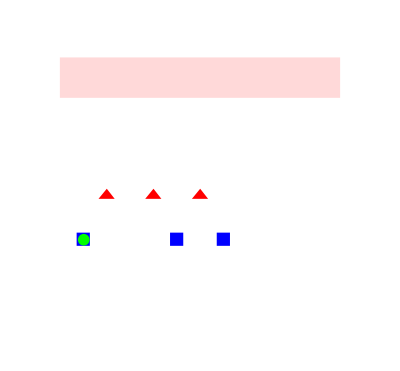
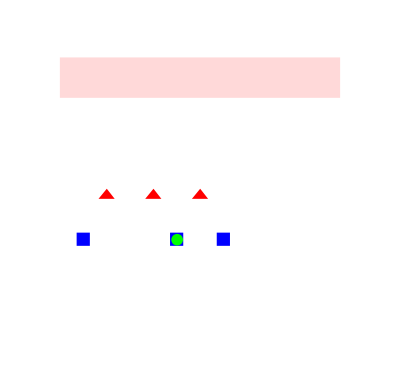
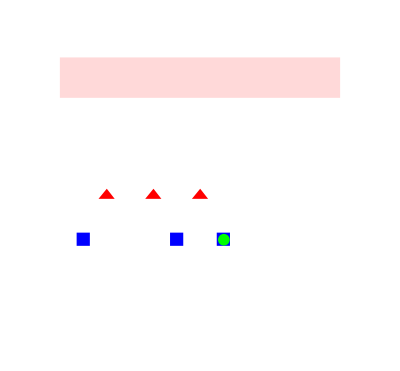

```mathematica
overlayAttackingMove[#, play3[[8]]]&/@ ams
```

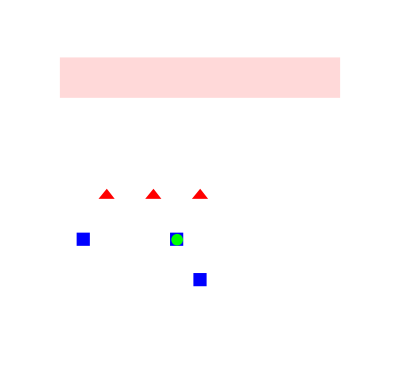

```mathematica
showGame@play3[[8]]
```

TODO: write function getFurthestAttacking that ignores interceptions. This will allow the defense to position themselves better.

```mathematica
getBestGame[play3[[8]]]
```

{{{{3/2,2 √3},{3,(3 √3)/2},{4,(3 √3)/2}},{{3/2,1/10+2 √3},{5/2,1/10+2 √3},{7/2,1/10+2 √3}},{3,(3 √3)/2},β,0,0},{{{1,(3 √3)/2},{3,(3 √3)/2},{4,(3 √3)/2}},{{3/2,1/10+2 √3},{5/2,1/10+2 √3},{7/2,1/10+2 √3}},{1,(3 √3)/2},β,0,0},{{{3/2,2 √3},{3,(3 √3)/2},{4,(3 √3)/2}},{{3/2,1/10+2 √3},{5/2,1/10+2 √3},{7/2,1/10+2 √3}},{4,(3 √3)/2},β,0,0}}

{{1,(3 √3)/2},{3,(3 √3)/2},{4,(3 √3)/2},{1,(3 √3)/2}}

{{{1,(3 √3)/2},{3,(3 √3)/2},{7/2,√3}},{{2,1/10+(5 √3)/2},{3/2,1/10+2 √3},{9/2,1/10+2 √3}},{3,(3 √3)/2},α,0,0}

```mathematica
g= {{{1,(3 √3)/2},{3,(3 √3)/2},{4,(3 √3)/2}},{{3/2,1/10+2 √3},{5/2,1/10+2 √3},{7/2,1/10+2 √3}},{3,(3 √3)/2},"β",0,0};
```

```mathematica
ams =moveAttackers[g, getGameInfo[g] ]
```

{{{3/2,2 √3},{3,(3 √3)/2},{9/2,2 √3},{9/2,2 √3}},{{3/2,2 √3},{3,(3 √3)/2},{7/2,2 √3},{3,(3 √3)/2}},{{1,(3 √3)/2},{3,(3 √3)/2},{7/2,2 √3},{1,(3 √3)/2}}}

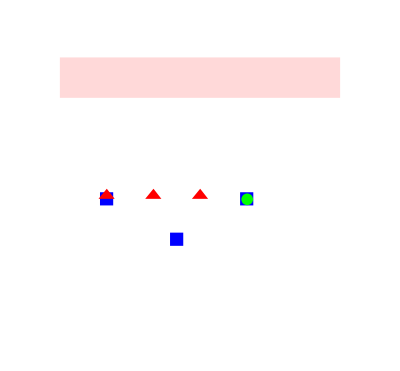
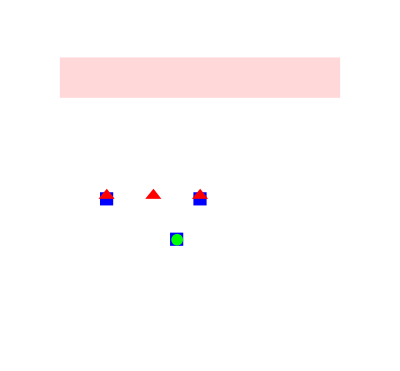
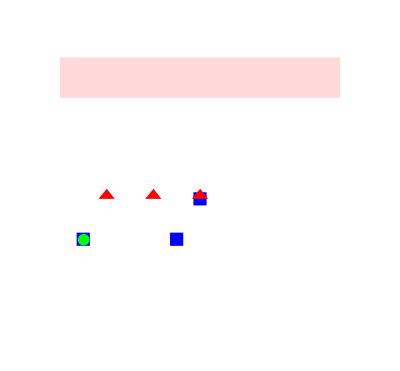

```mathematica
overlayAttackingMove[#, g]&/@ ams
```

```mathematica
play3 = getPlay[initialGameState, 20, getBestGame];
```

```mathematica
showGame@ play3[[8]]
```

-Graphics-

```mathematica
showPlay[play3]
```

#### Testing timing

```mathematica
gameState = initialGameState;
```

```mathematica
gs2 = getBestMove[gameState]
```

{{{2,(√3)/2},{7/2,√3},{4,(√3)/2}},{{2,1/10+(7 √3)/2},{3,1/10+(7 √3)/2},{4,1/10+(7 √3)/2}},{7/2,√3},β,0,0}

```mathematica
ginfo = getGameInfo[gameState];  // RepeatedTiming
```

{0.00118236,Null}

```mathematica
amoves = moveAttackers[gameState,ginfo, 10]; // RepeatedTiming
```

{0.0272475,Null}

```mathematica
(*Echo[overlayAttackingMove[#, gameState]&/@ amoves];*)
AssociateTo[ginfo, "passLocs"-> getPassLocs[ginfo, amoves[[All, -1]]]];
(*Echo@amoves;*)
```

```mathematica
ags = getAttackerGameState[#,gameState]&/@ amoves; // RepeatedTiming
```

{0.000351155,Null}

```mathematica
gi = getGameInfo[gs2]
```

<|had→-1/10,turn→β,bmoves→{{2,1/10+(√3)/2},{3,1/10+(√3)/2},{4,1/10+(√3)/2},{5,1/10+(√3)/2},{3/2,1/10+√3},{5/2,1/10+√3},{7/2,1/10+√3},{9/2,1/10+√3},{11/2,1/10+√3},{2,1/10+(3 √3)/2},{3,1/10+(3 √3)/2},{4,1/10+(3 √3)/2},{5,1/10+(3 √3)/2},{5/2,1/10+2 √3},{7/2,1/10+2 √3},{9/2,1/10+2 √3}},defenders→{{2,1/10+(7 √3)/2},{3,1/10+(7 √3)/2},{4,1/10+(7 √3)/2}},attackers→{{2,(√3)/2},{7/2,√3},{4,(√3)/2}},pg→2,pgLoc→{7/2,√3},aturn→α,aoffball→{{2,(√3)/2},{4,(√3)/2}},turntype→defender|>

```mathematica
AssociateTo[gi, "passLocs"-> getPassLocs[gi, amoves[[All, -1]]]];
```

```mathematica
bdm = moveDefenders[gs2,gi]; // RepeatedTiming
```

{0.036679,Null}

```mathematica
getDefenderGameState[bdm, gameState]
```

```mathematica
bgs = getBestGames[initialGameState]; // RepeatedTiming
```

{0.0373634,Null}

```mathematica
getBestGames/@ bgs; // RepeatedTiming
```

{0.387247,Null}

```mathematica
NestList[replaceGames,initialGameState, 3]; // RepeatedTiming
```

{0.537772,Null}

## Running Code

### Gameplay V2

```mathematica
getBestMove@initialGameState
```

{{{2,(√3)/2}},{{5/2,√3},{7/2,√3},{3,(√3)/2}},{{4,(√3)/2}}}

{{{2,(√3)/2},{5/2,√3},{4,(√3)/2}},{{2,1/10+(7 √3)/2},{3,1/10+(7 √3)/2},{4,1/10+(7 √3)/2}},{5/2,√3},β,0,0}

```mathematica
play2 = getPlay[initialGameState, 30, getBestMove];
```

```mathematica
showPlay[play2, ImageSize->400]
```

### Gameplay

```mathematica
play = getPlay[initialGameState, 30];
```

```mathematica
sp = showPlay[play,ImageSize->400]
```

### Court

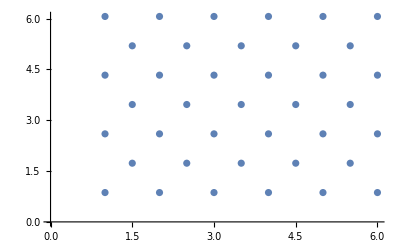

```mathematica
courtWidth = 5;
courtLength =6;
endzone = Rectangle[{1/2, (courtLength+1/2)(Sqrt[3]/2)}, {courtWidth+3/2, (courtLength+3/2)(Sqrt[3]/2)}];
directions = NestList[#+60Degree&, 0Degree, 6];
bottomLeftPoint = {1, 1};
background = Rectangle[bottomLeftPoint - {1, 1/2}, {courtWidth+2, courtLength+1}];
p = getPoint[bottomLeftPoint, 60Degree, 1]; 
{shortRowOffset, rowDiff} =p - bottomLeftPoint;
longRows = Table[NestList[getPoint[#, 0, 1]&, 
{bottomLeftPoint[[1]], (i - bottomLeftPoint[[2]]+ 1)*rowDiff},
 courtWidth], 
{i, bottomLeftPoint[[2]], courtLength+1, 2}];
shortRows = Table[NestList[getPoint[#, 0, 1]&, {p[[1]], (i - p[[2]]+2)*rowDiff}, courtWidth-1], {i, p[[2]], courtLength+1, 2}];
homeLocs = Riffle[longRows, shortRows];
homeAwayDistance = 1/10;
awayLocs = getAwayPoints[homeLocs, homeAwayDistance];
homeEndZoneY = homeLocs[[-1, 1, 2]];
awayEndZoneY = awayLocs[[1,1, 2]];
allLocs = Flatten[Join[homeLocs, awayLocs], 1];
gamePoly = BoundingRegion[allLocs, "MinConvexPolygon"];
ListPlot[Tooltip[#, #]&/@ Flatten[homeLocs, 1]]
```

### Object Parameters

```mathematica
playerSize = 1/5;
ballSize = 1/8;
playerSpeed = 1;
ballSpeed= 2;
stealDifficulty = 1;
```

### Initialization

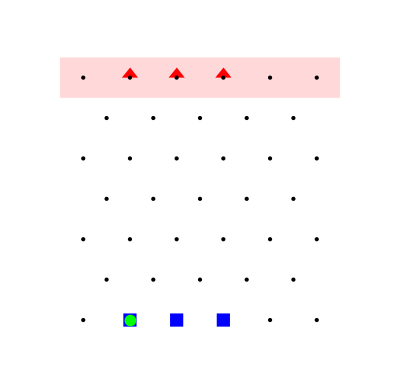

```mathematica
awayPlayers = getAwayPlayers[2, 1, 3];
homePlayers = getHomePlayers[2, 1, 3];
allPlayers = Join[homePlayers, awayPlayers];
turn = "α";
ballStart = 1;
ballLoc = getPlayerLoc["home", ballStart];
initialGuardCount = 0;
initialResult = 0;
initialGameState = {homePlayers, awayPlayers, ballLoc, turn, initialGuardCount, initialResult};
showGame[initialGameState, points->homeLocs]
```

## Data Analysis

### Ball Tracking

```mathematica
trackBall[games_]:= Module[{ballLocs}, 
ballLocs = games[[All, 3]];
ListLinePlot[ballLocs, PlotRange->{{1, courtWidth+1}, {1, courtLength*rowDiff+1}}, PlotHighlighting->None, ImageSize->Small,  Epilog->Style[endzone, Thickness[0.2], LightRed]]
]
```

```mathematica
trackBallList[playList_]:= Module[{ballLocsList}, 
ballLocsList = #[[All, 3]]&/@ playList;
ListLinePlot[ballLocsList, PlotRange->{{1, courtWidth+1}, {1, courtLength*rowDiff+1}}, PlotHighlighting->None, ImageSize->Large,  Epilog->Style[endzone, Thickness[0.2], LightRed], ImageSize->Medium]
]
```

```mathematica
trackOffense[games_]:= Module[{ballLocs, attackers, individual, labels}, 
ballLocs = games[[All, 3]];
attackers = games[[All, 1]];
individual = Transpose[attackers];
labels = StringJoin["p",ToString@#]& /@ Range[Length@attackers[[1]]];
ListLinePlot[Prepend[individual, ballLocs], PlotRange->{{1, courtWidth+1}, {1, courtLength*rowDiff+1}}, PlotLegends->Prepend[labels, "ball"], PlotHighlighting->None]
]
```

### Simulating Games

```mathematica
simPlays[n_:3]:= Module[{meta, plays}, 
meta = <|"CourtSize"->{courtLength, courtWidth}, "nHome"->Length@homePlayers, "nAway"->Length@awayPlayers, "ballSpeed"->ballSpeed|>;
plays = Table[getPlay[initialGameState, 50], n];
Prepend[plays, meta]
]
```

```mathematica
p1 = simPlays[5];
```

```mathematica
p1[[1]]
```

<|CourtSize→{6,5},nHome→2,nAway→3,ballSpeed→5|>

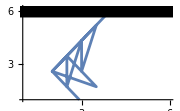
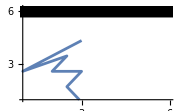
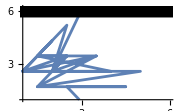
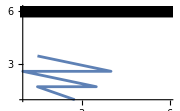
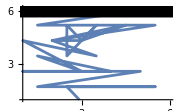

```mathematica
trackBall/@ Rest[p1]
```